## Basic Equations

### In cgs unit system

Maxwell’s equations:
- Quasi-neutrality
∑_s q_s n_s=∑_s q_s∫ⅆ^3 𝕧 f_s=0, where n_s is particle number density,
so ρ_e=q_e n_e=-∑_(s≠e) q_s n_s=-ρ_i, where ρ_i is the total ion charge density;
n_e=ρ_e/q_e=-ρ_i/q_e=-∑_(s≠e) q_s/q_e n_s.
- Ampere’s law
𝕛=∑_s q_s n_s 𝕦_s=∑_s q_s∫ⅆ^3 𝕧 𝕧 f_s=c/(4π)∇×𝔹, where 𝕛 is the current density and 𝕦_s is the mean velocity of species s,
so 𝕛_e=ρ_e 𝕦_e=q_e n_e 𝕦_e=𝕛-∑_(s≠e) q_s n_s 𝕦_s=𝕛-𝕛_i, where 𝕛_i is the total ion current density;
𝕦_e=𝕛_e/ρ_e=(𝕛-𝕛_i)/ρ_e=-(𝕛-𝕛_i)/ρ_i.
- Faraday’s law
(∂𝔹)/(∂t)=-c∇×𝔼.
- Divergence free
∇·𝔹=0.

Electron dynamics:
The electrons are assumed to be Maxwellian, gyrotropic.
The electric field can be written in terms of 𝕦_e, 𝔹, and n_e via the generalized Ohm’s law
𝔼+𝕦_e/c×𝔹-(4π)/c^2 η 𝕛=(∇p_e)/ρ_e,
where a simple model for the electron collision operator is adopted by introducing the magnetic diffusivity η,
which has units of length squared times frequency (l^2 s^-1). 
For adiabatic evolution, p_e=(p_(e,0)(n_e/n_(e,0)))^γ, where γ=5/3, or for isothermal (T_e=const), p_e=T_e n_e.
This can be written in terms of ρ_i, 𝕛_i, and 𝔹 using the quasi-neutrality condition
𝔼-(𝕛-𝕛_i)/(ρ_i c)×𝔹-(4π)/c^2 η 𝕛=-(∇p_e)/ρ_i.
Ion dynamics:
(∂𝕩_p)/(∂t)=𝕧_p,
(∂𝕧_p)/(∂t)=q_s/(m_s c)(c 𝔼-(4π)/c η 𝕛+𝕧_p×𝔹)=q_s/(m_s c)(c 𝔼-η∇×𝔹+𝕧_p×𝔹).
Current advance:
(∂𝕁_i)/(∂t)=∑_s q_s n_s 𝕧_s=∑_s q_s^2/(m_s c)n_s(c 𝔼-(4π)/c η 𝕛+𝕧_s×𝔹)=∑_s q_s/(m_s c)ρ_s(c 𝔼-(4π)/c η 𝕛+𝕧_s×𝔹).

Plasma beta of species s:
β_s=(8π n_s T_s)/B_0^2=ω_s^2/Ω_s^2(2 T_s)/(m_s c^2).

Energy density of fields:
u=1/(4π)(𝔼^2/2+𝔹^2/2).
Likewise, we define kinetic energy density of particles of species, s:
w=∑_s w_s, w_s=⟨(m_s 𝕧^2)/2⟩, where ⟨…⟩ denotes moment of the quantity.
Then the total energy in the system is
U=∫_V (u+w)ⅆV.

Poynting theorem:
1/(8π)(∂(𝔼^2+𝔹^2))/(∂t)+∇·𝕊=-𝕛·𝔼, where 𝕊=c/(4π)𝔼×𝔹.
The first term is the electromagnetic field energy density, and the third term is the mechanical energy.

### Simulation unit system

Change of variables:
q_0/(m_0 c)E=Ξ (frequency unit),
q_0/(m_0 c)B=Ω (frequency unit),
(4π q_0)/(m_0 c)J_s=𝒥_s (frequency squared unit),
(4π q_0)/m_0 ρ_s=Π_s (frequency squared unit),
(4π q_0^2)/(m_0^2 c^2)p_s=(4π q_0^2)/(m_0^2 c^2)T_s n_s=𝓅_s (frequency squared unit; pressure is energy density),
where Ω_0 is magnitude of the background magnetic field, Ω_s is the species cyclotron frequency and ω_s is the (initial) species plasma frequency.
Here ω_s^2=Ω_s/Ω_0 Π_s.
There is no need to introduce normalized diffusivity.

Quasi-neutrality
Π_e=-∑_(s≠e) Π_s=-Π_i.
Ampere’s law
c∇×Ω⃗=𝒥⃗,
(𝒥⃗)_e=𝒥⃗-∑_(s≠e) (𝒥⃗)_s=𝒥⃗-(𝒥⃗)_i,
𝕦_e/c=(𝒥⃗)_e/Π_e=(𝒥⃗-(𝒥⃗)_i)/Π_e=-(𝒥⃗-(𝒥⃗)_i)/Π_i.
Faraday’s law
∂Ω⃗/∂t=-c∇×Ξ⃗.

Electron dynamics:
Ξ⃗+𝕦_e/c×Ω⃗-η/c^2 𝒥⃗=c(∇𝓅_e)/Π_e → Ξ⃗=1/Π_i((𝒥⃗-(𝒥⃗)_i)×Ω⃗-c∇𝓅_e)+η/c^2 𝒥⃗.
Ion dynamics:
∂𝕩_p/∂t=𝕧_p,
∂𝕧_p/∂t=Ω_s/Ω_0(c(Ξ⃗-η/c^2 𝒥⃗)+𝕧_p×Ω⃗)=Ω_s/Ω_0(c Ξ⃗-η∇×Ω⃗+𝕧_p×Ω⃗).
Current advance:
(∂𝒥_i)/(∂t)=∑_s Π_s/c Ω_s/Ω_0(c(Ξ-η/c^2 𝒥)+𝕧_s×Ω)=∑_s (Ω_s/Ω_0 Π_s(Ξ-η/c^2 𝒥)+Ω_s/Ω_0 Π_s 𝕧_s/c×Ω)=Λ_i(Ξ-η/c^2 𝒥)+Γ_i×Ω.

Energy density of fields:
ε_EM=(Ξ^2+Ω^2)/2, where ε_EM=(4π q_0^2)/(m_0^2 c^2)u (frequency squared).
Likewise, we define kinetic energy density of particles of species, s:
ε_KE=∑_s ε_s (frequency squared unit), where ε_s=(4π q_0^2)/(m_0^2 c^2)w_s=(4π q_0^2)/(m_0^2 c^2)⟨(m_s 𝕧^2)/2⟩=(4π q_s^2)/(m_s c^2)Ω_0^2/Ω_s^2⟨𝕧^2/2⟩=Ω_0^2/Ω_s^2 ω_s^2/c^2(∑_j^(N^t) 𝕧_j^2/2)/N^0.
Then the total energy in the system is
ℰ=∫_V (ε_EM+ε_KE)ⅆV.

Poynting theorem:
Define the normalized Poynting vector: (4π q_0^2)/(m_0^2 c^2)S=𝒮.
Then 𝒮⃗=c Ξ⃗×Ω⃗, and 1/2(∂(Ξ^2+Ω^2))/(∂t)+∇·𝒮⃗=-𝒥⃗·Ξ⃗.

### In generalized curvilinear coordinates

- Quasi-neutrality
Π_e=-∑_(s≠e) Π_s=-Π_i.
- Ampere’s law
(𝒥)^i=c e^ijk(∂Ω_k)/(∂x^j),
- Faraday’s law
(∂Ω^i)/(∂t)=-c e^ijk(∂Ξ_k)/(∂x^j),
where e^ijk=ϵ^ijk/√g and g=|g_ij|.

Electron dynamics:
Ξ_i=η/c^2(𝒥)_i+c/Π_e(∂𝓅_e)/(∂x^i)-e_ijk/c(u_e)^j Ω^k → Ξ_i=η/c^2(𝒥)_i+1/Π_i(e_ijk((𝒥)^j-(𝒥_i)^j)Ω^k-c(∂𝓅_e)/(∂x^i)),
where e_ijk=√g ϵ^ijk.
Ion dynamics:
∂x^i/∂t=v^i,
∂𝕧_p/∂t=Ω_s/Ω_0(c(Ξ⃗-η/c^2 𝒥⃗)+𝕧_p×Ω⃗) (in Cartesian).
Current advance (since no spatial derivative, update in Cartesian may be easier):
(∂𝒥_i)/(∂t)=∑_s Π_s/c Ω_s/Ω_0(c(Ξ-η/c^2 𝒥)+𝕧_s×Ω)=∑_s (Ω_s/Ω_0 Π_s(Ξ-η/c^2 𝒥)+Ω_s/Ω_0 Π_s 𝕧_s/c×Ω)=Λ_i(Ξ-η/c^2 𝒥)+Γ_i×Ω (in Cartesian).
(∂(𝒥_i)_i)/(∂t)=Λ_i(Ξ_i-η/c^2(𝒥)_i)+(e_ijk(Γ_i))^j Ω^k.

Energy density of fields:
ε_EM=(Ξ^2+Ω^2)/2, where ε_EM=(4π q_0^2)/(m_0^2 c^2)u (frequency squared).
Likewise, we define kinetic energy density of particles of species, s:
ε_KE=∑_s ε_s (frequency squared unit), where ε_s=(4π q_0^2)/(m_0^2 c^2)w_s=(4π q_0^2)/(m_0^2 c^2)⟨(m_s 𝕧^2)/2⟩=(4π q_s^2)/(m_s c^2)Ω_0^2/Ω_s^2⟨𝕧^2/2⟩=Ω_0^2/Ω_s^2 ω_s^2/c^2(∑_j^(N^t) 𝕧_j^2/2)/N^0.
Then the total energy in the system is
ℰ=∫_V (ε_EM+ε_KE)ⅆV.

## Update Cycle

### Cycle (Kunz’s PC)

0. Deposit charge and current densities 𝕛_i^0 and ρ_i^0 and Ohm’s law 𝔼^0=𝔼(𝔹^0,ρ_i^0,𝕛_i^0).
1. Faraday’s law 𝔹_(pred,1)^(n+1)=𝔹^n-c Δt(∇×𝔼^n).
2. Ohm’s law 𝔼_(pred,1)^(n+1)=𝔼(𝔹_(pred,1)^(n+1),ρ_i^n,𝕛_i^n).
3. Time-centered electromagnetic fields
𝔹_(pred,1)^(n+1/2)=(𝔹^n+𝔹_(pred,1)^(n+1))/2 and
𝔼_(pred,1)^(n+1/2)=(𝔼^n+𝔼_(pred,1)^(n+1))/2.
4. Particle push
- 𝕩_i^*=𝕩_i^n+Δt/2 𝕧_i^n
- 𝕧_(i,pred)^(n+1)=𝕧_i^n+q_i/(m_i c)Δt(c 𝔼_(pred,1)^(n+1/2)-(4π)/c η 𝕛_(pred,1)^(n+1/2)+𝕧_i^n×𝔹_(pred,1)^(n+1/2))
- 𝕩_(i,pred)^(n+1)=𝕩_i^*+Δt/2 𝕧_(i,pred)^(n+1).
5. Deposit charge and current densities 𝕛_(i,pred)^(n+1) and ρ_(i,pred)^(n+1).
6. Faraday’s law 𝔹_(pred,2)^(n+1)=𝔹^n-c Δt(∇×𝔼_(pred,1)^(n+1/2)).
7. Ohm’s law 𝔼_(pred,2)^(n+1)=𝔼(𝔹_(pred,2)^(n+1),ρ_(i,pred)^(n+1),𝕛_(i,pred)^(n+1)).
8. Time-centered electromagnetic fields
𝔹_(pred,2)^(n+1/2)=(𝔹^n+𝔹_(pred,2)^(n+1))/2 and
𝔼_(pred,2)^(n+1/2)=(𝔼^n+𝔼_(pred,2)^(n+1))/2.
9. Particle push
- 𝕩_i^*=𝕩_i^n+Δt/2 𝕧_i^n
- 𝕧_i^(n+1)=𝕧_i^n+q_i/(m_i c)Δt(c 𝔼_(pred,2)^(n+1/2)-(4π)/c η 𝕛_(pred,2)^(n+1/2)+𝕧_i^n×𝔹_(pred,2)^(n+1/2))
- 𝕩_i^(n+1)=𝕩_i^*+Δt/2 𝕧_i^(n+1).
10. Deposit charge and current densities 𝕛_i^(n+1) and ρ_i^(n+1).
11. Faraday’s law 𝔹^(n+1)=𝔹^n-c Δt(∇×𝔼_(pred,2)^(n+1/2)).
12. Ohm’s law 𝔼^(n+1)=𝔼(𝔹^(n+1),ρ_i^(n+1),𝕛_i^(n+1)).

- Snapshots are only needed for 𝔹^n, 𝕧_i^n and 𝕩_i^n.

### Cycle (Matthews’ CAM-CL)

0. Initially given are 𝕩_i^0, 𝕧_i^(-1/2), 𝔹^0, and 𝔼^0.
1. Advance 𝕧_i^(n-1/2) to 𝕧_i^(n+1/2) and collect the moments:
𝕧_i^(n+1/2)=𝕧_i^(n-1/2)+q_i/(m_i c)Δt(c 𝔼^n-(4π)/c η 𝕛^n+𝕧_i^(n-1/2)×𝔹^n),
ρ_i^n=ρ_i(𝕩_i^n),
𝕛_i^-=𝕛(𝕩_i^n,𝕧_i^(n+1/2)).
2. Advance 𝕩_i^n to 𝕩_i^(n+1) and collect the moments:
𝕩_i^(n+1)=𝕩_i^n+Δt 𝕧_i^(n+1/2),
ρ_i^(n+1)=ρ_i(𝕩_i^(n+1)),
𝕛_i^+=𝕛(𝕩_i^(n+1),𝕧_i^(n+1/2)),
Λ_i^(n+1)=Λ(𝕩_i^(n+1)),
Γ_i^(n+1)=Γ(𝕩_i^(n+1),𝕧_i^(n+1/2)).
3. ρ_i^(n+1/2) and 𝕛_i^(n+1/2) are obtained as averages:
ρ_i^(n+1/2)=1/2(ρ_i^n+ρ_i^(n+1)),
𝕛_i^(n+1/2)=1/2(𝕛_i^-+𝕛_i^+).
4. 𝔹^n is advanced to 𝔹^(n+1) by subcycling:
𝔹^(n+1)=𝔹^n-c∫_n^(n+1) ∇×𝔼(𝔹(t),ρ_i^(n+1/2),𝕛_i^(n+1/2))ⅆt.
5. Advance 𝕛_i^+ to 𝕛_i^(n+1):
𝔼^*=𝔼(𝔹^(n+1),ρ_i^(n+1),𝕛_i^(n+1/2)) (resistivity subtracted),
𝕛_i^(n+1)=𝕛_i^++Δt/2(Λ_i^(n+1)𝔼^*+Γ_i^(n+1)×𝔹^(n+1)).
6. evaluate 𝔼^(n+1):
𝔼^(n+1)=𝔼(𝔹^(n+1),ρ_i^(n+1),𝕛_i^(n+1)).

- Snapshots: 𝔹^(n+1), 𝔼_i^(n+1), 𝕧_i^(n+1/2) and 𝕩_i^(n+1).

Cyclical scheme for magnetic field update subcycling:
𝔼_p=𝔼[ρ_i^(n+1/2),𝕁_i^(n+1/2),𝔹_p] and 𝔹_p=𝔹^(n+p/m) and δt=Δt/m with m subcycles.
𝔹_1=𝔹_0-c δt∇×𝔼_0,
𝔹_2=𝔹_0-2c δt∇×𝔼_1,
𝔹_(p+1)=𝔹_(p-1)-2c δt∇×𝔼_p, where p = 1, ..., m-1,
𝔹_m=𝔹_(m-2)-2c δt∇×𝔼_(m-1),
𝔹_m^*=𝔹_(m-1)-c δt∇×𝔼_m, and finally
𝔹^(n+1)=1/2(𝔹_m+𝔹_m^*).

## Discretization

Faraday’s law:
(∂Ω^1/∂t
∂Ω^2/∂t
∂Ω^3/∂t)=-c/(√g)(∂Ξ_3/∂x^2-∂Ξ_2/∂x^3
∂Ξ_1/∂x^3-∂Ξ_3/∂x^1
∂Ξ_2/∂x^1-∂Ξ_1/∂x^2),
Ampere’s law:
((𝒥)^1
(𝒥)^2
(𝒥)^3)=c/(√g)(∂Ω_3/∂x^2-∂Ω_2/∂x^3
∂Ω_1/∂x^3-∂Ω_3/∂x^1
∂Ω_2/∂x^1-∂Ω_1/∂x^2),
Generalized Ohm’s law:
(Ξ_1
Ξ_2
Ξ_3)=η/c^2((𝒥)_1
(𝒥)_2
(𝒥)_3)+c/Π_e(∂𝓅_e/∂x^1
∂𝓅_e/∂x^2
∂𝓅_e/∂x^3)-(√g)/c((u_e)^2 Ω^3-(u_e)^3 Ω^2
(u_e)^3 Ω^1-(u_e)^1 Ω^3
(u_e)^1 Ω^2-(u_e)^2 Ω^1) →
(Ξ_1
Ξ_2
Ξ_3)=η/c^2((𝒥)_1
(𝒥)_2
(𝒥)_3)+1/Π_i(√g(((𝒥)^2-(𝒥_i)^2)Ω^3-((𝒥)^3-(𝒥_i)^3)Ω^2
((𝒥)^3-(𝒥_i)^3)Ω^1-((𝒥)^1-(𝒥_i)^1)Ω^3
((𝒥)^1-(𝒥_i)^1)Ω^2-((𝒥)^2-(𝒥_i)^2)Ω^1)-c(∂𝓅_e/∂x^1
∂𝓅_e/∂x^2
∂𝓅_e/∂x^3)).

Equations of motion (non-relativistic):
(∂x^1/∂t
∂x^2/∂t
∂x^3/∂t)=(v^1
v^2
v^3),
(∂v_x/∂t
∂v_y/∂t
∂v_z/∂t)=Ω_s/Ω_0(c(Ξ_x-η/c^2(𝒥)_x)+v_y Ω_z-v_z Ω_y
c(Ξ_y-η/c^2(𝒥)_y)+v_z Ω_x-v_x Ω_z
c(Ξ_z-η/c^2(𝒥)_z)+v_x Ω_y-v_y Ω_x).

Current advance:
(∂(𝒥_i)_x/∂t
∂(𝒥_i)_y/∂t
∂(𝒥_i)_z/∂t)=Λ_i(Ξ_x-η/c^2(𝒥)_x
Ξ_y-η/c^2(𝒥)_y
Ξ_z-η/c^2(𝒥)_z)+((Γ_i)_y Ω_z-(Γ_i)_z Ω_y
(Γ_i)_z Ω_x-(Γ_i)_x Ω_z
(Γ_i)_x Ω_y-(Γ_i)_y Ω_x).

### 1D in x^1 direction

#### Simulation domain

Half integer grid: Ξ⃗, 𝒥⃗, (𝒥⃗)_e, (𝒥⃗)_i, Π_i, P_e, ∇P_e, Λ_i, Γ_i, all discrete particle moments, and 𝕍_f.
Full integer grid: Ω⃗ and δn_f.
Legend below:
- Red: Full grid
- Blue: Half grid
- Open circle: Ghost grid point
- Rectangle: Simulation box; simulation particles are bounded by this box.

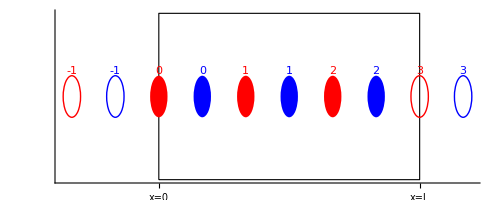

```mathematica
With[{L=3},
Show[
Graphics[{
{EdgeForm[Directive[Black]],FaceForm[Directive[Opacity[0]]],Rectangle[{0,-.4},{L,.4}]},
{Red,Disk[{#,0},.1]&/@Range[0,L-1],Circle[{-1,0},.1],Circle[{L,0},.1]},
{Red,Text[#,{#,+.1},{0,-1}]&/@Range[-1,L]},
{Blue,Disk[{#+.5,0},.1]&/@Range[0,L-1],Circle[{-1+.5,0},.1],Circle[{L+.5,0},.1]},
{Blue,Text[#,{#+.5,.1},{0,-1}]&/@Range[-1,L]}
}],
Axes->{True,False},
Ticks->{{{0,"\!\(x=0\)"},{L,"\!\(x=L\)"}},None},
BaseStyle->13
]
]
```

#### Magnetic field update

(ΔΩ^1/Δt
ΔΩ^2/Δt
ΔΩ^3/Δt)=-c/(√g)(0
-ΔΞ_3^t/Δx^1
ΔΞ_2^t/Δx^1)

(Ω_(t+Δt)^(1;i)
Ω_(t+Δt)^(2;i)
Ω_(t+Δt)^(3;i))=(Ω_t^(1;i)
Ω_t^(2;i)
Ω_t^(3;i))-(c Δt)/(√g Δx^1)(0
-(Ξ_(3;i)^t-Ξ_(3;i-1)^t)
+(Ξ_(2;i)^t-Ξ_(2;i-1)^t))

After update, calculate covariant components:
Ω_i=Ω^j g_ij;
(Ω_1
Ω_2
Ω_3)=(g_11 Ω^1+g_12 Ω^2+g_13 Ω^3
g_21 Ω^1+g_22 Ω^2+g_23 Ω^3
g_31 Ω^1+g_32 Ω^2+g_33 Ω^3);
and Cartesian components:
(Ω_x
Ω_y
Ω_z)=(Ω^1(g⃗)_1·(ê)_x+Ω^2(g⃗)_2·(ê)_x+Ω^3(g⃗)_3·(ê)_x
Ω^1(g⃗)_1·(ê)_y+Ω^2(g⃗)_2·(ê)_y+Ω^3(g⃗)_3·(ê)_y
Ω^1(g⃗)_1·(ê)_z+Ω^2(g⃗)_2·(ê)_z+Ω^3(g⃗)_3·(ê)_z)

#### Total current

(𝒥^1
𝒥^2
𝒥^3)=c/(√g)(0
-ΔΩ_3/Δx^1
ΔΩ_2/Δx^1)

(𝒥_t^(1;i)
𝒥_t^(2;i)
𝒥_t^(3;i))=c/(√g Δx^1)(0
-(Ω_(3;i+1)^t-Ω_(3;i)^t)
+(Ω_(2;i+1)^t-Ω_(2;i)^t))

After update, calculate covariant components:
𝒥_i=𝒥^j g_ij;
(𝒥_1
𝒥_2
𝒥_3)=(g_11 𝒥^1+g_12 𝒥^2+g_13 𝒥^3
g_21 𝒥^1+g_22 𝒥^2+g_23 𝒥^3
g_31 𝒥^1+g_32 𝒥^2+g_33 𝒥^3).

#### Electric field update

(Ξ_1
Ξ_2
Ξ_3)=η/c^2((𝒥)_1
(𝒥)_2
(𝒥)_3)+c/Π_e(∂𝓅_e/∂x^1
∂𝓅_e/∂x^2
∂𝓅_e/∂x^3)-(√g)/c((u_e)^2 Ω^3-(u_e)^3 Ω^2
(u_e)^3 Ω^1-(u_e)^1 Ω^3
(u_e)^1 Ω^2-(u_e)^2 Ω^1).

(Π_e)_i=-(Π_i)_i;
((𝒥⃗)_e)^i=(𝒥⃗)^i-((𝒥⃗)_i)^i;
(𝕦_e)^i/c=((𝒥⃗)_e)^i/((Π_e)_i);
Ω_full^i=1/2(Ω^(i+1)+Ω^i);
c/Π_e(∇𝓅_e)_i=1/Π_e c/(2 Δx^1)(𝓅_(e;i+1)-𝓅_(e;i-1)
0
0);

Update electric field:
(Ξ_(1;i)
Ξ_(2;i)
Ξ_(3;i))-η/c^2((𝒥)_(1;i)
(𝒥)_(2;i)
(𝒥)_(3;i))=c/Π_e((∇𝓅_e)_(1;i)
(∇𝓅_e)_(2;i)
(∇𝓅_e)_(3;i))-(√g)/c((u_e)^(2;i)Ω_full^(3;i)-(u_e)^(3;i)Ω_full^(2;i)
(u_e)^(3;i)Ω_full^(1;i)-(u_e)^(1;i)Ω_full^(3;i)
(u_e)^(1;i)Ω_full^(2;i)-(u_e)^(2;i)Ω_full^(1;i)).
After update, calculate Cartesian components of Ξ⃗-η/c^2 𝒥⃗:
(Ξ_x
Ξ_y
Ξ_z)=(Ξ_1(g⃗)^1·(ê)_x+Ξ_2(g⃗)^2·(ê)_x+Ξ_3(g⃗)^3·(ê)_x
Ξ_1(g⃗)^1·(ê)_y+Ξ_2(g⃗)^2·(ê)_y+Ξ_3(g⃗)^3·(ê)_y
Ξ_1(g⃗)^1·(ê)_z+Ξ_2(g⃗)^2·(ê)_z+Ξ_3(g⃗)^3·(ê)_z)

#### Position update

Cartesian to curvilinear:
(v^1
v^2
v^3)=(v_x(ê)_x·(g⃗)^1+v_y(ê)_y·(g⃗)^1+v_z(ê)_z·(g⃗)^1
v_x(ê)_x·(g⃗)^2+v_y(ê)_y·(g⃗)^2+v_z(ê)_z·(g⃗)^2
v_x(ê)_x·(g⃗)^3+v_y(ê)_y·(g⃗)^3+v_z(ê)_z·(g⃗)^3)

x_(t+Δt)^1=x_t^1+Δt v_(t+Δt/2)^1.

#### Velocity update in Cartesian coordinate

Step 0 - (Ξ_x[x_t^1]
Ξ_y[x_t^1]
Ξ_z[x_t^1])=∑_(i,j) (Ξ_(x;i)^t
Ξ_(y;i)^t
Ξ_(z;i)^t)S[x_t^1-Δx^1/2-x^(1;i)] and (Ω_x[x_t^1]
Ω_y[x_t^1]
Ω_z[x_t^1])=(Ω_x^0[x_t^1]
Ω_y^0[x_t^1]
Ω_z^0[x_t^1])+∑_i (δΩ_(x;i)^t
δΩ_(y;i)^t
δΩ_(z;i)^t)S[x_t^1-x^(1;i)],
Step 1 - (v_x^-
v_y^-
v_z^-)=(v_x^(t-Δt/2)
v_y^(t-Δt/2)
v_z^(t-Δt/2))+Ω_s/Ω_0(c Δt)/2(Ξ_x^t
Ξ_y^t
Ξ_z^t),
Step 2 - (v_x^0
v_y^0
v_z^0)=(v_x^-
v_y^-
v_z^-)+Ω_s/Ω_0 Δt/2(v_y^-Ω_z^t-v_z^-Ω_y^t
v_z^-Ω_x^t-v_x^-Ω_z^t
v_x^-Ω_y^t-v_y^-Ω_x^t),
Step 3 - (v_x^+
v_y^+
v_z^+)=(v_x^-
v_y^-
v_z^-)+Ω_s/Ω_0 Δt/2 2/(1+(Ω_s/Ω_0 Δt/2)^2((Ω_x^t)^2+(Ω_y^t)^2+(Ω_z^t)^2))(v_y^0 Ω_z^t-v_z^0 Ω_y^t
v_z^0 Ω_x^t-v_x^0 Ω_z^t
v_x^0 Ω_y^t-v_y^0 Ω_x^t), and
Step 4 - (v_x^(t+Δt/2)
v_y^(t+Δt/2)
v_z^(t+Δt/2))=(v_x^+
v_y^+
v_z^+)+Ω_s/Ω_0(c Δt)/2(Ξ_x^t
Ξ_y^t
Ξ_z^t).

#### Moments: from particle to grid

Number density (zeroth velocity moment) at ith grid point:
n_(t;s)^i=n_(0;s)^i(∑_p S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)])/(N_(c;s)^(0;i))=n_(0;s)(∑_p S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)])/(N_(c;s)), 
where 
N_(c;s)^0 is the initial number of simulation particles of species s at a reference cell; 
n_(0;s) is the initial number density of the species s at a reference cell; 
N_(c;s)^(0;i) is the initial number of simulation particles at (q^i) cell; and 
n_(0;s)^i is the initial number density at (q^i) cell.
Charge density at (q^i) cell is:
Π_t^i=∑_s Ω_0/Ω_s ω_(s;i)^2(∑_p S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)])/(N_(c;s)^(0;i))=∑_s Ω_0/Ω_s ω_(s;0)^2(∑_p S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)])/(N_(c;s)^0)=∑_s Ω_0/Ω_s ω_(s;0)^2(n_(t;s)^i)/(n_(0;s)),
where 
ω_(s;0) is the initial plasma frequency at the reference cell; and 
ω_(s;i)^2 is the initial plasma frequency at (q^i) cell.

```mathematica
With[{Nc=100,Nx=2,n0=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{x},
x=RandomReal[{0,1},Nc*Nx];
(Plus@@@S[x])/Nc
]]
```

Average flow speed weighted by n_(t;s)^i/n_(0;s):
(V_(x;i)^(t;s)
V_(y;i)^(t;s)
V_(z;i)^(t;s))=∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)]/(N_(c;s)^0)
Average flow speed is given by (V_(x;i)^(t;s)
V_(y;i)^(t;s)
V_(z;i)^(t;s))/(n_(t;s)^i)/(n_(0;s)).
Current density:
(𝒥_(x;i)^(t;s)
𝒥_(y;i)^(t;s)
𝒥_(z;i)^(t;s))=Ω_0/Ω_s(ω_(s;i)^2)/c∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)]/(N_(c;s)^(0;i))=Ω_0/Ω_s(ω_(s;0)^2)/c∑_p (v_(x;p)^(t;s)
v_(y;p)^(t;s)
v_(z;p)^(t;s))S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)]/(N_(c;s)^0)=Ω_0/Ω_s(ω_(s;0)^2)/c(V_(x;i)^(t;s)
V_(y;i)^(t;s)
V_(z;i)^(t;s))
Cartesian to curvilinear:
(𝒥^1
𝒥^2
𝒥^3)=(𝒥_x(ê)_x·(g⃗)^1+𝒥_y(ê)_y·(g⃗)^1+𝒥_z(ê)_z·(g⃗)^1
𝒥_x(ê)_x·(g⃗)^2+𝒥_y(ê)_y·(g⃗)^2+𝒥_z(ê)_z·(g⃗)^2
𝒥_x(ê)_x·(g⃗)^3+𝒥_y(ê)_y·(g⃗)^3+𝒥_z(ê)_z·(g⃗)^3)

```mathematica
Clear[icdf]
icdf:=icdf=With[{cdf=Function[v,-(2 ⅇ^(-v^2) v)/(√π)+Erf[v]],n=1000,vmax=4.},Interpolation[Table[{cdf[vmax i/n],vmax i/n},{i,0,n}]]]
```

```mathematica
Plot[icdf[i],{i,0,1},PlotRange->All]
```

```mathematica
With[{Nc=1000,Nx=2,n0=1.,θ=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{rng,x,v,vx,vy,vz,ψ},
rng:=RandomReal[{0,1},Nc*Nx];
x=rng;
v=icdf[rng]θ;
vx=v (ψ=1-2rng);
v=v √(1-ψ^2);
vy=v Cos[ψ=2π rng];
vz=v Sin[ψ];
TableForm[Function[v,{v//Mean,Mean[(Total[v#]&/@S[x])/Nc]n0}]/@{vx,vy,vz},TableHeadings->{{"v_x","v_y","v_z"},{"⟨𝕧⟩","2nd Mom × n_s^0"}}]
]]
```

Average second velocity moment weighted by n_(t;s)^i/n_(0;s):
(2 𝕨_s)/m_s=⟨𝕧_i^(t;s)𝕧_i^(t;s)⟩=n_(0;s)^i∑_p 𝕧_p^(t;s)𝕧_p^(t;s)S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)]/(N_(c;s)^(0;i))=n_(0;s)∑_p 𝕧_p^(t;s)𝕧_p^(t;s)S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)]/(N_(c;s)^0).
Kinetic energy density (equivalent to pressure):
ε_i^(t;s)=Ω_0^2/Ω_s^2(ω_(s;i)^2)/c^2∑_p 1/2(v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)]/(N_(c;s)^(0;i))=Ω_0^2/Ω_s^2(ω_(s;0)^2)/c^2∑_p 1/2(v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)]/(N_(c;s)^0).
Thermal speed squared:
⟨(Δv_(x,s;i)^2
Δv_(y,s;i)^2
Δv_(z,s;i)^2)⟩=(n_(0;s))/(n_(t;s)^i)(∑_p (v_(x;p)^2
v_(y;p)^2
v_(z;p)^2)S[x_(t;s)^(1;p)-Δx^1/2-x^(1;i)]/(N_(c;s)^0)-(V_(x;i)^(t;s)
V_(y;i)^(t;s)
V_(z;i)^(t;s))^2/(n_(t;s)^i)/(n_(0;s))).

```mathematica
With[{Nc=1000,Nx=2,n0=1.,θ=1.,S=Function[x(*0≤x≤1*),{1-x,x}//N]},Module[{rng,x,v,vx,vy,vz,ψ},
rng:=RandomReal[{0,1},Nc*Nx];
x=rng;
v=icdf[rng]θ;
vx=v (ψ=1-2rng);
v=v √(1-ψ^2);
vy=v Cos[ψ=2π rng];
vz=v Sin[ψ];
{Total[Flatten[{vx,vy,vz}^2]]/2,
Total[Total[(vx^2+vy^2+vz^2)#/2]/Nc&/@S[x]]*Nc}
]]
```